## Kapitola 13 - Shlukování dat sítí bez učitele

Demonstrace použití neuronové sítě bez učitele k hledání shluků v datech.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Vytvoření trénovacích dat

Vygenerujeme si data, na kterých budeme prezentovat shlukování. Protože pracujeme se sítí bez učitele, postačí nám vstupní data a nepotřebujeme generovat žádná výstupní data.

```mathematica
values=10;
(* hodnoty ve {,} udávají x-ový a y-ový rozsah každého shluku *)
cluster1x =RandomReal[{-0.1,0.1},{values,1}];cluster1y=RandomReal[ {-0.1,0.1},{values,1}];
cluster2x =RandomReal[{-0.1,0.1},{values,1}];cluster2y=RandomReal[ {0.9,1.1},{values,1}];
cluster3x =RandomReal[{0.3,0.5},{values,1}];cluster3y=RandomReal[ {1.4,1.6},{values,1}];
cluster4x =RandomReal[{0.9,1.1},{values,1}];cluster4y=RandomReal[ {2.1,1.9},{values,1}];
cluster5x =RandomReal[{1.4,1.6},{values,1}];cluster5y=RandomReal[ {1.4,1.6},{values,1}];
cluster6x =RandomReal[{1.9,2.1},{values,1}];cluster6y=RandomReal[ {1.1,0.9},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inData= Join[cluster1,cluster2,cluster3,cluster4,cluster5,cluster6];
```

Vygenerovaná data jsou dvoudimenzionální a obsahují 6 jasně oddělených shluků.

Data si můžeme zobrazit zde.

```mathematica
inData
```

{{-0.0514963,0.0208927},{-0.0912566,-0.0985843},{-0.0662185,-0.0884734},{-0.0815643,-0.0714254},{0.0119118,0.0522096},{-0.0166724,0.0148136},{0.0569589,-0.0918037},{-0.0943064,0.0396653},{-0.0690079,-0.0260895},{-0.00346203,-0.0968413},{-0.0479021,0.950009},{0.0652212,1.08974},{0.0398772,0.900956},{0.0377568,1.09997},{0.0548625,1.06606},{-0.0837789,1.03216},{0.0422369,1.01475},{-0.0117965,1.05508},{-0.000591322,1.08429},{0.0201324,1.08482},{0.344941,1.44666},{0.476943,1.54056},{0.394625,1.40298},{0.452147,1.4464},{0.434294,1.48774},{0.444209,1.56628},{0.496812,1.477},{0.421796,1.4485},{0.368719,1.59626},{0.356787,1.50917},{1.09071,1.96115},{1.06444,2.01933},{1.05154,1.94433},{0.924839,2.0294},{0.906994,1.98276},{1.09585,1.9405},{0.970125,1.98896},{0.958259,2.04654},{0.9375,2.05967},{1.04919,1.90486},{1.46147,1.51988},{1.45461,1.48509},{1.52857,1.52729},{1.45975,1.40275},{1.43508,1.50636},{1.5659,1.48297},{1.46974,1.59686},{1.45357,1.40944},{1.52186,1.533},{1.55535,1.54514},{1.98863,0.914987},{2.0815,0.990844},{2.05004,1.00998},{2.04533,0.969526},{1.92152,1.09881},{2.09548,1.02415},{1.98869,1.06325},{1.9816,1.08901},{2.09064,0.907611},{2.01611,1.06449}}

Pro lepší představu o struktuře dat si je můžeme zobrazit v grafu.

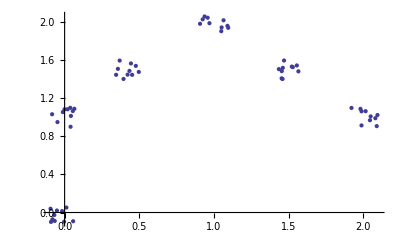

```mathematica
ListPlot[inData]
```

## Zpracování dat neuronovou sítí

Samoorganizující se neuronovou síť použijeme k hledání shluků ve vygenerovaných datech. Vytvoříme síť o šesti neuronech, kterou necháme na datech naučit. Po naučení sítě chceme aby ideálně každý neuron reprezentoval jeden shluk ve vstupních datech. Poté je možné spočítat hraničnípřímky mezi jednotlivými neurony a tím de facto rozdělit do požadovaného počtu shluků celý vstupní prostor.

### Náhodně inicializovaná síť

Nejprve vytvoříme neuronovou síť o šesti neuronech. Počet neuronů určuje kolik shluků se síť pokusí v datech najít.

```mathematica
unsup=InitializeUnsupervisedNet[inData,6];
```

Tuto neuronovou síť naučíme na našich datech

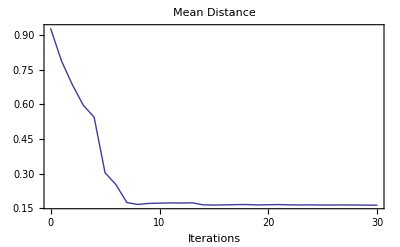

UnsupervisedNet::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{unsup,fitrecord}=UnsupervisedNetFit[inData,unsup,30,ReportFrequency->1];
```

Vidíme že během učení sítě jeden z neuronů “zemřel”, tzn. není použit k rozlišení shluků v datech. Později se mu ještě budeme věnovat.

Ilustraci jaým způsobem byla data rozdělena do shluků nám poskytne následující graf. Pozice neuronu, který reprezentuje daný shluk je naznačena tučným číslem. Je také jasně vidět, který neuron je “mrtvý” a nepřináší nám žádný užitek.

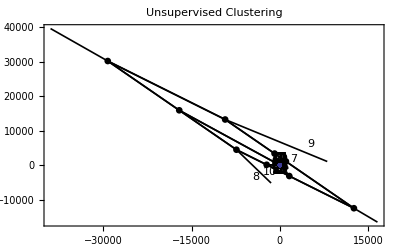

```mathematica
NetPlot[unsup,inData,CbvSymbol->{FontSize->30}]
```

Můžeme také jednoduše nechat “oklasifikovat” nový vektor (zadáme jeho x a y souřadnici).

```mathematica
unsup[{0.2,0.7}]
```

{2}

Číslo, které nám síť vrátila znamená číselné označení shluku, kam vektor spadá (odpovídá číslům v grafu)

Nyní si vzpomeneme, že máme v síti nepotřebný neuron, budeme ho tedy chtít odstranit.
Nejdříve zjistíme o který neuron se jedná.

```mathematica
UnUsedNeurons[unsup,inData]
```

{6}

A poté ho odstraníme. Novou síť bez nepotřebného neuronu pojmenujeme unsup1.

```mathematica
unsup1=NeuronDelete[unsup,%]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2011, 5, 13, 9, 6, 31.1706024}, AccumulatedIterations → 30, SOM → None}]

Podíváme se jakým způsobem odděluje síť jednotlivé shluky po odebrání nepotřebného neuronu.

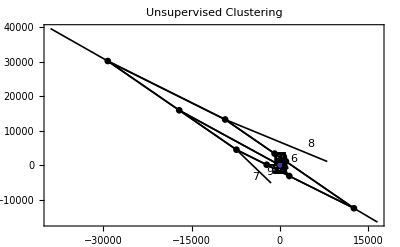

```mathematica
NetPlot[unsup1,inData,CbvSymbol->{FontSize->30}]
```

### Síť inicializovaná metodou SOM

Protože vidíme, že rozdělení dat na shluky ještě není perfektní můžeme se pokust dosáhnout ještě lepšího rozdělení. Místo náhodné inicializace sítě můžeme použít SOM (samoorganizující mapu) k inicializaci sítě. Samoorganizující mapa se nechá přizpůsobit datům, na souřadnicích, kde skončí její neurony, jsou inicializovány neurony naší požadované sítě (naše síť není SOM).

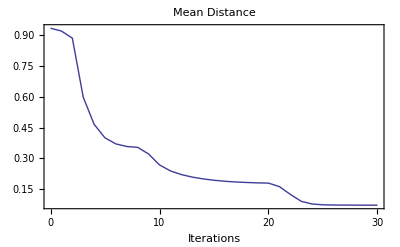

```mathematica
unsup2=InitializeUnsupervisedNet[inData,6,UseSOM ->True,CriterionPlot->True,CriterionLog->True,Iterations->30];
```

Nyní naučíme zinicializovanou síť na našich datech.

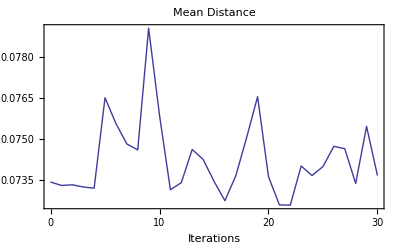

```mathematica
{unsup2,fitrecord2}=UnsupervisedNetFit[inData,unsup2,30];
```

A podíváme se jakým způsobem uřčuje shluky v datech.

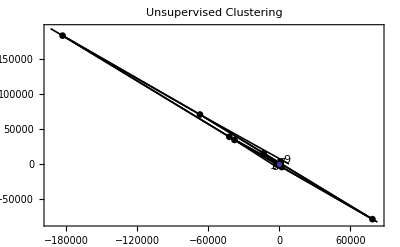

```mathematica
NetPlot[unsup2,inData]
```

Tento přístup k inicializaci sítě nám může často pomoci dosáhnout lepších výsledků, než náhodná inicializace. Také často zabrání problému s “mrtvými” neurony.

## Průběh učení

### Náhodně inicializovaná síť

Ještě se můžeme podívat jak síť v průběhu učení dělila data do shluků a jak se měnila poloha jednotlivých neuronů. Barevné čáry ukazují pohyb jednotlivých neuronů, čísla ukazují jejich konečnou polohu.

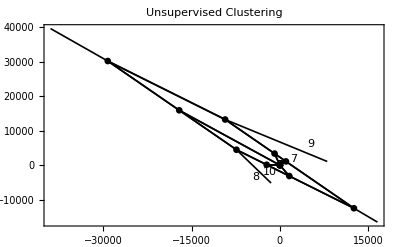

```mathematica
NetPlot[fitrecord,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState=NetPlot[fitrecord,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

### Síť inicializovaná metodou SOM

Z následujícího grafu je patrné, že i pouze zinicializovaná síť metodou SOM by poskytovala poměrně dobré výsledky a její učení upravuje pouze pozici několika neuronů.

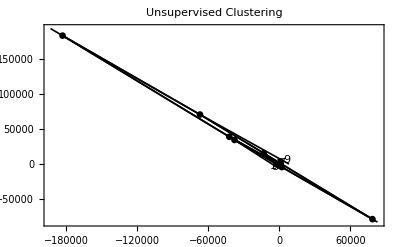

```mathematica
NetPlot[fitrecord2,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState2=NetPlot[fitrecord2,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState2[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.